```mathematica
Range[0,3]
```

{0,1,2,3}

```mathematica
Maximize[{
Total[-Binomial[3,#]p[#]Log[p[#]]&/@Range[0,3]],
Fold[And,True,{
Total[Binomial[3,#]p[#]&/@Range[0,3]]==1
}~Join~(p[#]≥0&/@Range[0,3])
]},p/@Range[0,3]]
```

Maximize[{-Log[p[0]] p[0]-3 Log[p[1]] p[1]-3 Log[p[2]] p[2]-Log[p[3]] p[3],p[0]+3 p[1]+3 p[2]+p[3]==1&&p[0]≥0&&p[1]≥0&&p[2]≥0&&p[3]≥0},{p[0],p[1],p[2],p[3]}]

```mathematica
pat=Solve[{
p[0]+3p[1]+3p[2]+p[3]==1,
-p[0]-p[1]+p[2]+p[3]==e,
p[0]-p[1]-p[2]+p[3]==P},{p[1],p[2],p[3]}][[1]]
```

{p[1]→1/4 (1-2 e+P-4 p[0]),p[2]→1/2 (e-P+2 p[0]),p[3]→1/4 (1+3 P-4 p[0])}

```mathematica
{p[1]≥0,p[2]≥0,p[3]≥0}//.pat
```

{1/4 (1-2 e+P-4 p[0])≥0,1/2 (e-P+2 p[0])≥0,1/4 (1+3 P-4 p[0])≥0}

```mathematica
{p[1]+p[2],p[3]+p[2]}//.pat//Simplify
```

{(1-P)/4,1/4 (1+2 e+P)}

```mathematica
Total[-Binomial[3,#]p[#]Log[p[#]]&/@Range[0,3]]
h=(%//.pat//FullSimplify[#,Assumptions->{(1-P)/4≥0,1/4 (1+2 e+P)≥0}]&)
```

-Log[p[0]] p[0]-3 Log[p[1]] p[1]-3 Log[p[2]] p[2]-Log[p[3]] p[3]

1/4 (-3 Log[1/4 (1-2 e+P-4 p[0])] (1-2 e+P-4 p[0])-4 Log[p[0]] p[0]-6 Log[(e-P)/2+p[0]] (e-P+2 p[0])+Log[1/4 (1+3 P-4 p[0])] (-1-3 P+4 p[0]))

```mathematica
xpat=Solve[D[h,p[0]]==0,{p[0]},Reals]
```

{{p[0]→ConditionalExpression[Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1],(-1<e≤-1/3&&-1-2 e<P<1)||(-1/3<e≤1/3&&-1/3<P<1)||(1/3<e<1&&-1+2 e<P<1)]}}

```mathematica
feas=Reduce[(1-P≥0)&&((1+2 e+P)≥0)&&((-1<e≤-1/3&&-1-2 e<P<1)||(-1/3<e≤1/3&&-1/3<P<1)||(1/3<e<1&&-1+2 e<P<1))]
```

-1/3<P<1&&1/2 (-1-P)<e<(1+P)/2

```mathematica
FullSimplify[Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1],Assumptions->feas]
```

$Aborted

```mathematica
InputForm
```

Root[-108 + 5103*#1 - 
   30870*#1^2 + 480200*#1^3 & , 
 1, 0]

```mathematica
psol=Join[{p[0]->p0},pat//.{p[0]->p0}]//FullSimplify
```

{p[0]→Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1],p[1]→1/4 (1-2 e+P-4 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1]),p[2]→(e-P)/2+Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1],p[3]→1/4 (1+3 P-4 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1])}

```mathematica
FullSimplify[Fold[And,True,psol//.(a_->b_):>(a==b)],Assumptions->(p[#]≥0)&/@{0,1,2,3}]
```

p[0]==Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1]&&1+P==2 e+4 p[1]+4 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1]&&e+2 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1]==P+2 p[2]&&4 (p[3]+Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1])==1+3 P

```mathematica
%/.e->0
```

p[0]==Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1]&&1+P==4 p[1]+4 Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1]&&2 Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1]==P+2 p[2]&&4 (p[3]+Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1])==1+3 P

```mathematica
FullSimplify[%,Assumptions->(p[#]≥0&/@{0,1,2,3})]
```

p[0]==Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1]&&1+P==4 (p[1]+Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1])&&P+2 p[2]==2 Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1]&&4 (p[3]+Root[-1-6 P-12 P^2-10 P^3-3 P^4+(16+72 P+96 P^2+8 P^3) #1+(-96-288 P) #1^2+256 #1^3&,1])==1+3 P

```mathematica
r=-p[0]+3p[1]-3p[2]+p[3]//.psol//FullSimplify
```

1-3 e+3 P-8 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1]

```mathematica
r//RootReduce
```

1-3 e+3 P-8 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1]

```mathematica
rnow=(r/.{e->1/7,P->2/5}//FullSimplify)
```

Root0.0945Root[-2546+27258 #1-7350 #1^2+42875 #1^3&,1]0.0944842233389854

```mathematica
rN=rnow//N
```

0.0944842

```mathematica
rra=(rN//RootApproximant)
```

Root0.0945Root[1-11 #1+4 #1^2+9 #1^3-47 #1^4-34 #1^5+39 #1^6&,1]0.09448422333898188

```mathematica
rra//InputForm
```

Root[1 - 11*#1 + 4*#1^2 + 
   9*#1^3 - 47*#1^4 - 34*#1^5 + 
   39*#1^6 & , 1, 0]

```mathematica
rnow//InputForm
```

Root[-2546 + 27258*#1 - 
   7350*#1^2 + 42875*#1^3 & , 
 1, 0]

```mathematica
SetOptions[Roots,Cubics->False]
```

{Cubics→False,Eliminate→False,EquatedTo→Null,Modulus→0,Multiplicity→1,Quartics→True,Using→True}

```mathematica
Solve[-2546+27258*#1-7350*#1^2+42875*#1^3&[x]==0,x]
```

{{x→Root0.0945Root[-2546+27258 #1-7350 #1^2+42875 #1^3&,1]0.0944842233389854},{x→Root0.0385-0.792 ⅈRoot[-2546+27258 #1-7350 #1^2+42875 #1^3&,2]0.03847217404479314},{x→Root0.0385+0.792 ⅈRoot[-2546+27258 #1-7350 #1^2+42875 #1^3&,3]0.03847217404479314}}

```mathematica
_□
```

```mathematica
RootReduce[rnow]//InputForm
```

Root[-2546 + 27258*#1 - 
   7350*#1^2 + 42875*#1^3 & , 
 1, 0]

```mathematica
0.0944842233389854
```

```mathematica
?RootReduce
```

```mathematica
feas
```

-1/3<P<1&&1/2 (-1-P)<e<(1+P)/2

```mathematica
Reduce[(R==r)&&feas]
```

((-1<e≤-1/3&&-1-2 e<P<1)||(-1/3<e≤1/3&&-1/3<P<1)||(1/3<e<1&&-1+2 e<P<1))&&R==1-3 e+3 P-8 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1]

```mathematica
re =(r/.e->1/3//RootReduce//FullSimplify)
```

3 P-8 Root[-1-12 P-54 P^2-108 P^3-81 P^4+(72+72 P+1944 P^2+216 P^3) #1-6912 P #1^2+6912 #1^3&,1]

```mathematica
feas/.e->1/3//Reduce
```

-1/3<P<1

```mathematica
FullSimplify[re,Assumptions->(feas/.e->1/3//Reduce)]
```

3 P-8 Root[-1-12 P-54 P^2-108 P^3-81 P^4+(72+72 P+1944 P^2+216 P^3) #1-6912 P #1^2+6912 #1^3&,1]

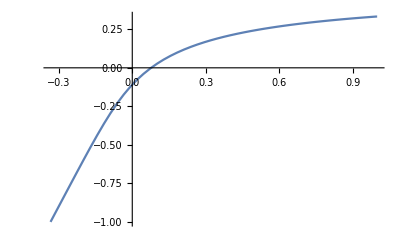

```mathematica
Plot[re,{P,-1/3,1}]
```

```mathematica
Series[re,{P,0,3}]
```

AlgebraicNumber-0.109AlgebraicNumber[Root[-2+6 #1+#1^3&,1],{0,-1/3,0}]-0.10916000069110877+AlgebraicNumber1.70AlgebraicNumber[Root[-2+6 #1+#1^3&,1],{5/3,0,1/3}]1.7024143839193153 P+AlgebraicNumber-4.11AlgebraicNumber[Root[-2+6 #1+#1^3&,1],{-4,0,-1}]-4.107243151757946 P^2+AlgebraicNumber4.76AlgebraicNumber[Root[-2+6 #1+#1^3&,1],{4,2,1}]4.762203155904598 P^3+O[P]^4

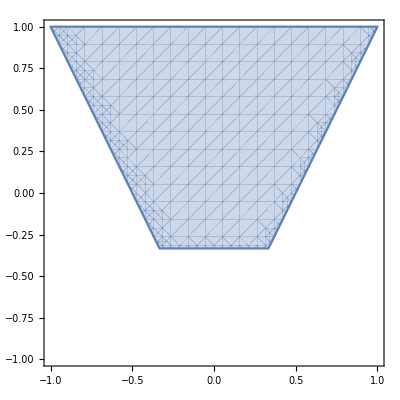

```mathematica
RegionPlot[feas,{e,-1,1},{P,-1,1}]
```

```mathematica
N[%/.P->1]
```

2.88658×10^-15

```mathematica
?Piecewise
```

```mathematica
FullSimplify[1-3 e+3 P-8 Root[-1+6 e-12 e^2+8 e^3-6 P+30 e P-48 e^2 P+24 e^3 P-12 P^2+42 e P^2-36 e^2 P^2-10 P^3+18 e P^3-3 P^4+(16-72 e+96 e^2+72 P-240 e P+96 e^2 P+96 P^2-72 e P^2+8 P^3) #1+(-96+288 e-288 P+96 e P) #1^2+256 #1^3&,1],Assumptions->
```